```mathematica
<<Notation`;
```

```mathematica
Symbolize[u^t]; Symbolize[(u̇)^t]; Symbolize[(u^(..))^t]; Symbolize[u^(t+Δt)]; Symbolize[(u̇)^(t+Δt)]; Symbolize[(u^(..))^(t+Δt)]; Symbolize[u^(t+γΔt)]; Symbolize[(u̇)^(t+γΔt)]; Symbolize[(u^(..))^(t+γΔt)]; Symbolize[Subscript[β, 1]]; Symbolize[Subscript[β, 2]] ; Symbolize[Subscript[a, k]]; Symbolize[Subscript[n, x]]; Symbolize[Subscript[n, t]]; Symbolize[Subscript[u, 1]^(t+Δt)]; Symbolize[Subscript[u, 2]^(t+Δt)]; Symbolize[Subscript[u, 3]^(t+Δt)]; Symbolize[Subscript[u, 4]^(t+Δt)]; Symbolize[Subscript[u, 5]^(t+Δt)]; Symbolize[Subscript[u, 6]^(t+Δt)]; Symbolize[Subscript[u, 1]^(t+γΔt)]; Symbolize[Subscript[u, 2]^(t+γΔt)]; Symbolize[Subscript[u, 3]^(t+γΔt)]; Symbolize[Subscript[u, 4]^(t+γΔt)]; Symbolize[Subscript[u, 5]^(t+γΔt)]; Symbolize[Subscript[u, 6]^(t+γΔt)]; Symbolize[Subscript[u, 1]^t]; Symbolize[Subscript[u, 2]^t]; Symbolize[Subscript[u, 3]^t]; Symbolize[Subscript[u, 4]^t]; Symbolize[Subscript[u, 5]^t]; Symbolize[Subscript[u, 0]^1]; Symbolize[Subscript[u, 1]^1]; Symbolize[Subscript[u, 2]^1]; Symbolize[Subscript[u, 0]^(1/2)]; Symbolize[Subscript[u, 1]^(1/2)]; Symbolize[Subscript[u, 2]^(1/2)]; Symbolize[Subscript[u, 0]^0]; Symbolize[Subscript[u, 1]^0];  Symbolize[Subscript[u, 2]^0];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
γ=1/2;Subscript[β, 2]=2 Subscript[β, 1];
```

```mathematica
eq1=m(u^(..))^t+ Subscript[c, 0]^2 k u^t==0;
eq2=m(u^(..))^(t+γΔt)+Subscript[c, 0]^2 k u^(t+γΔt)==0;
eq3=m(u^(..))^(t+Δt)+Subscript[c, 0]^2 k u^(t+Δt)==0;
eq4=u^(t+γΔt)==u^t+(γ Δt)/2((u̇)^t+(u̇)^(t+γΔt));
eq5=(u̇)^(t+γΔt)==(u̇)^t+(γ Δt)/2((u^(..))^t+(u^(..))^(t+γΔt));
eq6=u^(t+Δt)==u^t+γ Δt((1-Subscript[β, 1])(u̇)^t+Subscript[β, 1](u̇)^(t+γΔt))+(1-γ)Δt((1-Subscript[β, 2])(u̇)^(t+γΔt)+Subscript[β, 2](u̇)^(t+Δt));
eq7=(u̇)^(t+Δt)==(u̇)^t+γ Δt((1-Subscript[β, 1])(u^(..))^t+Subscript[β, 1](u^(..))^(t+γΔt))+(1-γ)Δt((1-Subscript[β, 2])(u^(..))^(t+γΔt)+Subscript[β, 2](u^(..))^(t+Δt));
```

```mathematica
lmf=Collect[Eliminate[{eq1,eq2,eq3,eq4,eq5,eq6,eq7},{(u^(..))^t,(u^(..))^(t+γΔt),(u^(..))^(t+Δt),(u̇)^t,(u̇)^(t+γΔt),(u̇)^(t+Δt)}]//FullSimplify,{u^t,u^(t+γΔt),u^(t+Δt)}]
```

u^t (8 m+k β_1 Δt^2 c_0^2+k β_2 Δt^2 c_0^2-2 k β_1 β_2 Δt^2 c_0^2)+u^(t+γΔt) (-16 m+k β_1 Δt^2 c_0^2+k β_2 Δt^2 c_0^2+2 k β_1 β_2 Δt^2 c_0^2-2 k β_2^2 Δt^2 c_0^2)+u^(t+Δt) (8 m+2 k β_2^2 Δt^2 c_0^2)==0

```mathematica
m=Δx/6({{1, 4, 1}});
```

```mathematica
k=1/Δx({{-1, 2, -1}});
```

```mathematica
Δt=(cfl Δx)/Subscript[c, 0];
```

```mathematica
u^(t+Δt)=({{Subscript[u, 0]^1}, {Subscript[u, 1]^1}, {Subscript[u, 2]^1}});u^(t+γΔt)=({{Subscript[u, 0]^(1/2)}, {Subscript[u, 1]^(1/2)}, {Subscript[u, 2]^(1/2)}});u^t=({{Subscript[u, 0]^0}, {Subscript[u, 1]^0}, {Subscript[u, 2]^0}});
```

```mathematica
Subscript[u, 0]^1=E^(I κ Δx (0-(Subscript[n, t]+1)((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))(*notice here, Subscript[n, x]=3 and Subscript[n, t]=0(koz t+0Δt)*)
```

ⅇ^(-(ⅈ c cfl (1+n_t) Δx κ)/c_0)

```mathematica
Subscript[u, 1]^1=E^(I κ Δx (1-(Subscript[n, t]+1)((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))
```

ⅇ^(ⅈ Δx κ (1-(c cfl (1+n_t))/c_0))

```mathematica
Subscript[u, 2]^1=E^(I κ Δx (2-(Subscript[n, t]+1)((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))
```

ⅇ^(ⅈ Δx κ (2-(c cfl (1+n_t))/c_0))

```mathematica
Subscript[u, 0]^(1/2)=E^(I κ Δx (0-(Subscript[n, t]+1/2)((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))(*notice here, Subscript[n, x]=3 and Subscript[n, t]=0(koz t+0Δt)*)
```

ⅇ^(-(ⅈ c cfl (1/2+n_t) Δx κ)/c_0)

```mathematica
Subscript[u, 1]^(1/2)=E^(I κ Δx (1-(Subscript[n, t]+1/2)((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))
```

ⅇ^(ⅈ Δx κ (1-(c cfl (1/2+n_t))/c_0))

```mathematica
Subscript[u, 2]^(1/2)=E^(I κ Δx (2-(Subscript[n, t]+1/2)((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))
```

ⅇ^(ⅈ Δx κ (2-(c cfl (1/2+n_t))/c_0))

```mathematica
Subscript[u, 0]^0=E^(I κ Δx (0-Subscript[n, t]((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))(*notice here, Subscript[n, x]=3 and Subscript[n, t]=0(koz t+0Δt)*)
```

ⅇ^(-(ⅈ c cfl n_t Δx κ)/c_0)

```mathematica
Subscript[u, 1]^0=E^(I κ Δx (1-Subscript[n, t]((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))
```

ⅇ^(ⅈ Δx κ (1-(c cfl n_t)/c_0))

```mathematica
Subscript[u, 2]^0=E^(I κ Δx (2-Subscript[n, t]((Subscript[c, 0] Δt)/Δx)(c/Subscript[c, 0])))
```

ⅇ^(ⅈ Δx κ (2-(c cfl n_t)/c_0))

```mathematica
lmf= (8 m+k Subscript[β, 1] Δt^2 Subscript[c, 0]^2+k Subscript[β, 2] Δt^2 Subscript[c, 0]^2-2 k Subscript[β, 1] Subscript[β, 2] Δt^2 Subscript[c, 0]^2).u^t+ (-16 m+k Subscript[β, 1] Δt^2 Subscript[c, 0]^2+k Subscript[β, 2] Δt^2 Subscript[c, 0]^2+2 k Subscript[β, 1] Subscript[β, 2] Δt^2 Subscript[c, 0]^2-2 k Subscript[β, 2]^2 Δt^2 Subscript[c, 0]^2).u^(t+γΔt)+ (8 m+2 k Subscript[β, 2]^2 Δt^2 Subscript[c, 0]^2).u^(t+Δt)==0
```

{{ⅇ^(ⅈ Δx κ (1-(c cfl n_t)/c_0)) ((16 Δx)/3+2 cfl^2 β_1 Δx+2 cfl^2 β_2 Δx-4 cfl^2 β_1 β_2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl n_t)/c_0)) ((4 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx+2 cfl^2 β_1 β_2 Δx)+ⅇ^(-(ⅈ c cfl n_t Δx κ)/c_0) ((4 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx+2 cfl^2 β_1 β_2 Δx)+ⅇ^(ⅈ Δx κ (1-(c cfl (1/2+n_t))/c_0)) (-(32 Δx)/3+2 cfl^2 β_1 Δx+2 cfl^2 β_2 Δx+4 cfl^2 β_1 β_2 Δx-4 cfl^2 β_2^2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl (1+n_t))/c_0)) ((4 Δx)/3-2 cfl^2 β_2^2 Δx)+ⅇ^(-(ⅈ c cfl (1+n_t) Δx κ)/c_0) ((4 Δx)/3-2 cfl^2 β_2^2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl (1/2+n_t))/c_0)) (-(8 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx-2 cfl^2 β_1 β_2 Δx+2 cfl^2 β_2^2 Δx)+ⅇ^(-(ⅈ c cfl (1/2+n_t) Δx κ)/c_0) (-(8 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx-2 cfl^2 β_1 β_2 Δx+2 cfl^2 β_2^2 Δx)+ⅇ^(ⅈ Δx κ (1-(c cfl (1+n_t))/c_0)) ((16 Δx)/3+4 cfl^2 β_2^2 Δx)}}==0

```mathematica
lmf=ⅇ^(ⅈ Δx κ (1-(c cfl Subscript[n, t])/Subscript[c, 0])) ((16 Δx)/3+2 cfl^2 Subscript[β, 1] Δx+2 cfl^2 Subscript[β, 2] Δx-4 cfl^2 Subscript[β, 1] Subscript[β, 2] Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl Subscript[n, t])/Subscript[c, 0])) ((4 Δx)/3-cfl^2 Subscript[β, 1] Δx-cfl^2 Subscript[β, 2] Δx+2 cfl^2 Subscript[β, 1] Subscript[β, 2] Δx)+ⅇ^(-(ⅈ c cfl Subscript[n, t] Δx κ)/Subscript[c, 0]) ((4 Δx)/3-cfl^2 Subscript[β, 1] Δx-cfl^2 Subscript[β, 2] Δx+2 cfl^2 Subscript[β, 1] Subscript[β, 2] Δx)+ⅇ^(ⅈ Δx κ (1-(c cfl (1/2+Subscript[n, t]))/Subscript[c, 0])) (-(32 Δx)/3+2 cfl^2 Subscript[β, 1] Δx+2 cfl^2 Subscript[β, 2] Δx+4 cfl^2 Subscript[β, 1] Subscript[β, 2] Δx-4 cfl^2 Subscript[β, 2]^2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl (1+Subscript[n, t]))/Subscript[c, 0])) ((4 Δx)/3-2 cfl^2 Subscript[β, 2]^2 Δx)+ⅇ^(-(ⅈ c cfl (1+Subscript[n, t]) Δx κ)/Subscript[c, 0]) ((4 Δx)/3-2 cfl^2 Subscript[β, 2]^2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl (1/2+Subscript[n, t]))/Subscript[c, 0])) (-(8 Δx)/3-cfl^2 Subscript[β, 1] Δx-cfl^2 Subscript[β, 2] Δx-2 cfl^2 Subscript[β, 1] Subscript[β, 2] Δx+2 cfl^2 Subscript[β, 2]^2 Δx)+ⅇ^(-(ⅈ c cfl (1/2+Subscript[n, t]) Δx κ)/Subscript[c, 0]) (-(8 Δx)/3-cfl^2 Subscript[β, 1] Δx-cfl^2 Subscript[β, 2] Δx-2 cfl^2 Subscript[β, 1] Subscript[β, 2] Δx+2 cfl^2 Subscript[β, 2]^2 Δx)+ⅇ^(ⅈ Δx κ (1-(c cfl (1+Subscript[n, t]))/Subscript[c, 0])) ((16 Δx)/3+4 cfl^2 Subscript[β, 2]^2 Δx)
```

ⅇ^(ⅈ Δx κ (1-(c cfl n_t)/c_0)) ((16 Δx)/3+2 cfl^2 β_1 Δx+2 cfl^2 β_2 Δx-4 cfl^2 β_1 β_2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl n_t)/c_0)) ((4 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx+2 cfl^2 β_1 β_2 Δx)+ⅇ^(-(ⅈ c cfl n_t Δx κ)/c_0) ((4 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx+2 cfl^2 β_1 β_2 Δx)+ⅇ^(ⅈ Δx κ (1-(c cfl (1/2+n_t))/c_0)) (-(32 Δx)/3+2 cfl^2 β_1 Δx+2 cfl^2 β_2 Δx+4 cfl^2 β_1 β_2 Δx-4 cfl^2 β_2^2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl (1+n_t))/c_0)) ((4 Δx)/3-2 cfl^2 β_2^2 Δx)+ⅇ^(-(ⅈ c cfl (1+n_t) Δx κ)/c_0) ((4 Δx)/3-2 cfl^2 β_2^2 Δx)+ⅇ^(ⅈ Δx κ (2-(c cfl (1/2+n_t))/c_0)) (-(8 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx-2 cfl^2 β_1 β_2 Δx+2 cfl^2 β_2^2 Δx)+ⅇ^(-(ⅈ c cfl (1/2+n_t) Δx κ)/c_0) (-(8 Δx)/3-cfl^2 β_1 Δx-cfl^2 β_2 Δx-2 cfl^2 β_1 β_2 Δx+2 cfl^2 β_2^2 Δx)+ⅇ^(ⅈ Δx κ (1-(c cfl (1+n_t))/c_0)) ((16 Δx)/3+4 cfl^2 β_2^2 Δx)

```mathematica
lmf/Δx*3//Simplify
```

ⅇ^(-(ⅈ c cfl (1+n_t) Δx κ)/c_0) (4-6 cfl^2 β_2^2)-2 ⅇ^(ⅈ Δx κ (2-(c cfl (1+n_t))/c_0)) (-2+3 cfl^2 β_2^2)+4 ⅇ^(ⅈ Δx κ (1-(c cfl (1+n_t))/c_0)) (4+3 cfl^2 β_2^2)+2 ⅇ^(ⅈ Δx κ (1-(c cfl (1/2+n_t))/c_0)) (-16+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(ⅈ Δx κ (2-(c cfl (1/2+n_t))/c_0)) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(-(ⅈ c cfl (1/2+n_t) Δx κ)/c_0) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-2 ⅇ^(ⅈ Δx κ (1-(c cfl n_t)/c_0)) (-8+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(ⅈ Δx κ (2-(c cfl n_t)/c_0)) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(-(ⅈ c cfl n_t Δx κ)/c_0) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))

```mathematica
ⅇ^(-(ⅈ c cfl (1+Subscript[n, t]) Δx κ)/Subscript[c, 0]) (4-6 cfl^2 Subscript[β, 2]^2)-2 ⅇ^(ⅈ Δx κ (2-(c cfl (1+Subscript[n, t]))/Subscript[c, 0])) (-2+3 cfl^2 Subscript[β, 2]^2)+4 ⅇ^(ⅈ Δx κ (1-(c cfl (1+Subscript[n, t]))/Subscript[c, 0])) (4+3 cfl^2 Subscript[β, 2]^2)+2 ⅇ^(ⅈ Δx κ (1-(c cfl (1/2+Subscript[n, t]))/Subscript[c, 0])) (-16+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(ⅈ Δx κ (2-(c cfl (1/2+Subscript[n, t]))/Subscript[c, 0])) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(-(ⅈ c cfl (1/2+Subscript[n, t]) Δx κ)/Subscript[c, 0]) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-2 ⅇ^(ⅈ Δx κ (1-(c cfl Subscript[n, t])/Subscript[c, 0])) (-8+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))+ⅇ^(ⅈ Δx κ (2-(c cfl Subscript[n, t])/Subscript[c, 0])) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))+ⅇ^(-(ⅈ c cfl Subscript[n, t] Δx κ)/Subscript[c, 0]) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))/.Δx κ-> ΔxκByπ Pi
```

ⅇ^(-(ⅈ c cfl (1+n_t) π ΔxκByπ)/c_0) (4-6 cfl^2 β_2^2)-2 ⅇ^(ⅈ π ΔxκByπ (2-(c cfl (1+n_t))/c_0)) (-2+3 cfl^2 β_2^2)+4 ⅇ^(ⅈ π ΔxκByπ (1-(c cfl (1+n_t))/c_0)) (4+3 cfl^2 β_2^2)+2 ⅇ^(ⅈ π ΔxκByπ (1-(c cfl (1/2+n_t))/c_0)) (-16+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(ⅈ π ΔxκByπ (2-(c cfl (1/2+n_t))/c_0)) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(-(ⅈ c cfl (1/2+n_t) π ΔxκByπ)/c_0) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-2 ⅇ^(ⅈ π ΔxκByπ (1-(c cfl n_t)/c_0)) (-8+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(ⅈ π ΔxκByπ (2-(c cfl n_t)/c_0)) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(-(ⅈ c cfl n_t π ΔxκByπ)/c_0) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))

```mathematica
ⅇ^(-(ⅈ c cfl (1+Subscript[n, t]) π ΔxκByπ)/Subscript[c, 0]) (4-6 cfl^2 Subscript[β, 2]^2)-2 ⅇ^(ⅈ π ΔxκByπ (2-(c cfl (1+Subscript[n, t]))/Subscript[c, 0])) (-2+3 cfl^2 Subscript[β, 2]^2)+4 ⅇ^(ⅈ π ΔxκByπ (1-(c cfl (1+Subscript[n, t]))/Subscript[c, 0])) (4+3 cfl^2 Subscript[β, 2]^2)+2 ⅇ^(ⅈ π ΔxκByπ (1-(c cfl (1/2+Subscript[n, t]))/Subscript[c, 0])) (-16+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(ⅈ π ΔxκByπ (2-(c cfl (1/2+Subscript[n, t]))/Subscript[c, 0])) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(-(ⅈ c cfl (1/2+Subscript[n, t]) π ΔxκByπ)/Subscript[c, 0]) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-2 ⅇ^(ⅈ π ΔxκByπ (1-(c cfl Subscript[n, t])/Subscript[c, 0])) (-8+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))+ⅇ^(ⅈ π ΔxκByπ (2-(c cfl Subscript[n, t])/Subscript[c, 0])) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))+ⅇ^(-(ⅈ c cfl Subscript[n, t] π ΔxκByπ)/Subscript[c, 0]) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))/.c/Subscript[c, 0]->cByc
```

ⅇ^(-ⅈ cByc cfl (1+n_t) π ΔxκByπ) (4-6 cfl^2 β_2^2)-2 ⅇ^(ⅈ (2-cByc cfl (1+n_t)) π ΔxκByπ) (-2+3 cfl^2 β_2^2)+4 ⅇ^(ⅈ (1-cByc cfl (1+n_t)) π ΔxκByπ) (4+3 cfl^2 β_2^2)+2 ⅇ^(ⅈ (1-cByc cfl (1/2+n_t)) π ΔxκByπ) (-16+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(-ⅈ cByc cfl (1/2+n_t) π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(ⅈ (2-cByc cfl (1/2+n_t)) π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-2 ⅇ^(ⅈ (1-cByc cfl n_t) π ΔxκByπ) (-8+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(-ⅈ cByc cfl n_t π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(ⅈ (2-cByc cfl n_t) π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))

```mathematica
nd=ⅇ^(-ⅈ cByc cfl (1+Subscript[n, t]) π ΔxκByπ) (4-6 cfl^2 Subscript[β, 2]^2)-2 ⅇ^(ⅈ (2-cByc cfl (1+Subscript[n, t])) π ΔxκByπ) (-2+3 cfl^2 Subscript[β, 2]^2)+4 ⅇ^(ⅈ (1-cByc cfl (1+Subscript[n, t])) π ΔxκByπ) (4+3 cfl^2 Subscript[β, 2]^2)+2 ⅇ^(ⅈ (1-cByc cfl (1/2+Subscript[n, t])) π ΔxκByπ) (-16+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(-ⅈ cByc cfl (1/2+Subscript[n, t]) π ΔxκByπ) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(ⅈ (2-cByc cfl (1/2+Subscript[n, t])) π ΔxκByπ) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-2 ⅇ^(ⅈ (1-cByc cfl Subscript[n, t]) π ΔxκByπ) (-8+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))+ⅇ^(-ⅈ cByc cfl Subscript[n, t] π ΔxκByπ) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))+ⅇ^(ⅈ (2-cByc cfl Subscript[n, t]) π ΔxκByπ) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))
```

ⅇ^(-ⅈ cByc cfl (1+n_t) π ΔxκByπ) (4-6 cfl^2 β_2^2)-2 ⅇ^(ⅈ (2-cByc cfl (1+n_t)) π ΔxκByπ) (-2+3 cfl^2 β_2^2)+4 ⅇ^(ⅈ (1-cByc cfl (1+n_t)) π ΔxκByπ) (4+3 cfl^2 β_2^2)+2 ⅇ^(ⅈ (1-cByc cfl (1/2+n_t)) π ΔxκByπ) (-16+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(-ⅈ cByc cfl (1/2+n_t) π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(ⅈ (2-cByc cfl (1/2+n_t)) π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-2 ⅇ^(ⅈ (1-cByc cfl n_t) π ΔxκByπ) (-8+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(-ⅈ cByc cfl n_t π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(ⅈ (2-cByc cfl n_t) π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))

```mathematica
eq=nd//Cancel//ExpandAll//Simplify
```

ⅇ^(-ⅈ cByc cfl (1+n_t) π ΔxκByπ) (4-6 cfl^2 β_2^2+ⅇ^(2 ⅈ π ΔxκByπ) (4-6 cfl^2 β_2^2)+4 ⅇ^(ⅈ π ΔxκByπ) (4+3 cfl^2 β_2^2)+ⅇ^(ⅈ (1+cByc cfl) π ΔxκByπ) (16+6 cfl^2 (β_1+β_2-2 β_1 β_2))+2 ⅇ^(1/2 ⅈ (2+cByc cfl) π ΔxκByπ) (-16+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(1/2 ⅈ cByc cfl π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(1/2 ⅈ (4+cByc cfl) π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))+ⅇ^(ⅈ cByc cfl π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(ⅈ (2+cByc cfl) π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2))))

```mathematica
nd2=4-6 cfl^2 Subscript[β, 2]^2+ⅇ^(2 ⅈ π ΔxκByπ) (4-6 cfl^2 Subscript[β, 2]^2)+4 ⅇ^(ⅈ π ΔxκByπ) (4+3 cfl^2 Subscript[β, 2]^2)+ⅇ^(ⅈ (1+cByc cfl) π ΔxκByπ) (16+6 cfl^2 (Subscript[β, 1]+Subscript[β, 2]-2 Subscript[β, 1] Subscript[β, 2]))+2 ⅇ^(1/2 ⅈ (2+cByc cfl) π ΔxκByπ) (-16+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(1/2 ⅈ cByc cfl π ΔxκByπ) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))-ⅇ^(1/2 ⅈ (4+cByc cfl) π ΔxκByπ) (8+3 cfl^2 (Subscript[β, 1]+Subscript[β, 2]+2 Subscript[β, 1] Subscript[β, 2]-2 Subscript[β, 2]^2))+ⅇ^(ⅈ cByc cfl π ΔxκByπ) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))+ⅇ^(ⅈ (2+cByc cfl) π ΔxκByπ) (4+cfl^2 (-3 Subscript[β, 2]+Subscript[β, 1] (-3+6 Subscript[β, 2])))//Cancel//ExpandAll//Simplify
```

4-6 cfl^2 β_2^2+ⅇ^(2 ⅈ π ΔxκByπ) (4-6 cfl^2 β_2^2)+4 ⅇ^(ⅈ π ΔxκByπ) (4+3 cfl^2 β_2^2)+ⅇ^(ⅈ (1+cByc cfl) π ΔxκByπ) (16+6 cfl^2 (β_1+β_2-2 β_1 β_2))+2 ⅇ^(1/2 ⅈ (2+cByc cfl) π ΔxκByπ) (-16+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(1/2 ⅈ cByc cfl π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))-ⅇ^(1/2 ⅈ (4+cByc cfl) π ΔxκByπ) (8+3 cfl^2 (β_1+β_2+2 β_1 β_2-2 β_2^2))+ⅇ^(ⅈ cByc cfl π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))+ⅇ^(ⅈ (2+cByc cfl) π ΔxκByπ) (4+cfl^2 (-3 β_2+β_1 (-3+6 β_2)))

```mathematica
Reduce=Solve[nd2==0, cByc]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::wrsym: Symbol Reduce is Protected.

{{cByc→-1/(cfl π ΔxκByπ)2 ⅈ Log[(8+32 ⅇ^(ⅈ π ΔxκByπ)+8 ⅇ^(2 ⅈ π ΔxκByπ)+3 cfl^2 β_1-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1+3 cfl^2 β_2-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2+6 cfl^2 β_1 β_2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2-6 cfl^2 β_2^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2^2-√(-4 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 β_1+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1-3 cfl^2 β_2+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2+6 cfl^2 β_1 β_2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2) (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-6 cfl^2 β_2^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2^2)+(-8-32 ⅇ^(ⅈ π ΔxκByπ)-8 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 β_1+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1-3 cfl^2 β_2+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2-6 cfl^2 β_1 β_2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 β_2^2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2^2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2^2)^2))/(2 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 β_1+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1-3 cfl^2 β_2+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2+6 cfl^2 β_1 β_2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2))]},{cByc→-1/(cfl π ΔxκByπ)2 ⅈ Log[(8+32 ⅇ^(ⅈ π ΔxκByπ)+8 ⅇ^(2 ⅈ π ΔxκByπ)+3 cfl^2 β_1-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1+3 cfl^2 β_2-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2+6 cfl^2 β_1 β_2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2-6 cfl^2 β_2^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2^2+√(-4 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 β_1+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1-3 cfl^2 β_2+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2+6 cfl^2 β_1 β_2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2) (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-6 cfl^2 β_2^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2^2)+(-8-32 ⅇ^(ⅈ π ΔxκByπ)-8 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 β_1+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1-3 cfl^2 β_2+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2-6 cfl^2 β_1 β_2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 β_2^2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2^2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2^2)^2))/(2 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 β_1+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1-3 cfl^2 β_2+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_2-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_2+6 cfl^2 β_1 β_2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) β_1 β_2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) β_1 β_2))]}}

```mathematica
Subscript[β, 1]=0.65;
```

```mathematica
cfl=2;
```

```mathematica
solu=-1/(cfl π ΔxκByπ)2 ⅈ Log[(8+32 ⅇ^(ⅈ π ΔxκByπ)+8 ⅇ^(2 ⅈ π ΔxκByπ)+3 cfl^2 Subscript[β, 1]-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]+3 cfl^2 Subscript[β, 2]-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]+6 cfl^2 Subscript[β, 1] Subscript[β, 2]-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]-6 cfl^2 Subscript[β, 2]^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]^2-√(-4 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 Subscript[β, 1]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 Subscript[β, 2]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]+6 cfl^2 Subscript[β, 1] Subscript[β, 2]-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]) (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-6 cfl^2 Subscript[β, 2]^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]^2)+(-8-32 ⅇ^(ⅈ π ΔxκByπ)-8 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 Subscript[β, 1]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 Subscript[β, 2]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]-6 cfl^2 Subscript[β, 1] Subscript[β, 2]+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 Subscript[β, 2]^2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]^2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]^2)^2))/(2 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 Subscript[β, 1]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 Subscript[β, 2]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]+6 cfl^2 Subscript[β, 1] Subscript[β, 2]-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]))];
```

```mathematica
plotb0p65CFL2p0=solu;
```

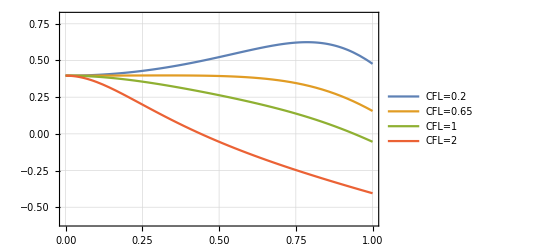

```mathematica
Plot[{Abs[plotb0p65CFL0p2]-1,Abs[plotb0p65CFL0p65]-1,Abs[plotb0p65CFL1p0]-1,Abs[plotb0p65CFL2p0]-1},{ΔxκByπ,0.000001,1},PlotRange->{-.6,.8},PlotLegends->LineLegend[{"CFL=0.2","CFL=0.65","CFL=1","CFL=2"},LegendFunction->(Framed[#]&)],PlotTheme->"Detailed"]
```

```mathematica
q1c=-1/(cfl π ΔxκByπ)2 ⅈ Log[(8+32 ⅇ^(ⅈ π ΔxκByπ)+8 ⅇ^(2 ⅈ π ΔxκByπ)+3 cfl^2 Subscript[β, 1]-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]+3 cfl^2 Subscript[β, 2]-6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]+3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]+6 cfl^2 Subscript[β, 1] Subscript[β, 2]-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]-6 cfl^2 Subscript[β, 2]^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]^2-√(-4 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 Subscript[β, 1]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 Subscript[β, 2]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]+6 cfl^2 Subscript[β, 1] Subscript[β, 2]-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]) (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-6 cfl^2 Subscript[β, 2]^2+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]^2-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]^2)+(-8-32 ⅇ^(ⅈ π ΔxκByπ)-8 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 Subscript[β, 1]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 Subscript[β, 2]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]-6 cfl^2 Subscript[β, 1] Subscript[β, 2]+12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]-6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 Subscript[β, 2]^2-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]^2+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]^2)^2))/(2 (4+16 ⅇ^(ⅈ π ΔxκByπ)+4 ⅇ^(2 ⅈ π ΔxκByπ)-3 cfl^2 Subscript[β, 1]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1]-3 cfl^2 Subscript[β, 2]+6 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 2]-3 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 2]+6 cfl^2 Subscript[β, 1] Subscript[β, 2]-12 cfl^2 ⅇ^(ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]+6 cfl^2 ⅇ^(2 ⅈ π ΔxκByπ) Subscript[β, 1] Subscript[β, 2]))];cfl//Clear;
```

```mathematica
cfl=.65;qc=FindRoot[ΔxκByπ π-(0.6 π)/(cfl Abs[q1c]),{ΔxκByπ,0.1}];qc=qc[[1,2]]
```

0.879327

```mathematica
cfl=1;qc=FindRoot[ΔxκByπ π-(0.6 π)/(cfl Abs[q1c]),{ΔxκByπ,0.1}];qc=qc[[1,2]]
```

0.470257

```mathematica
cfl=2;qc=FindRoot[ΔxκByπ π-(0.6 π)/(cfl Abs[q1c]),{ΔxκByπ,0.1}];qc=qc[[1,2]]
```

0.219873